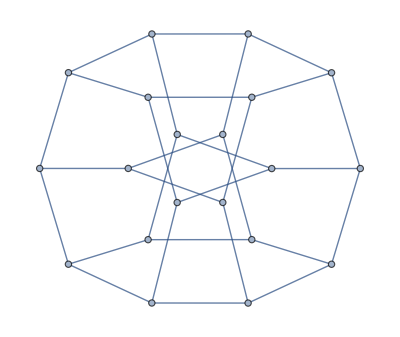

```mathematica
g=Graph[{11<->1,11<->4,11<->7,12<->2,12<->5,12<->7,13<->3,13<->6,13<->7,14<->8,14<->9,14<->10,15<->2,15<->3,15<->10,16<->1,16<->3,16<->9,17<->1,17<->2,17<->8,18<->5,18<->6,18<->10,19<->4,19<->5,19<->8,20<->4,20<->6,20<->9}]
```

```mathematica
FindHamiltonianCycle[g]
```

{{11<->7,7<->13,13<->3,3<->16,16<->9,9<->14,14<->10,10<->15,15<->2,2<->12,12<->5,5<->18,18<->6,6<->20,20<->4,4<->19,19<->8,8<->17,17<->1,1<->11}}